# CHSH Game: illustrating the peculiar advantages of quantum strategies over classical ones

Shivam Sawarn

This computational essay is about the CHSH game, a notable scenario within quantum mechanics, illustrating the peculiar advantages of quantum strategies over classical ones in particular computational contexts. The CHSH game, formulated from the CHSH inequality proposed in 1969, showcases intriguing quantum phenomena through a straightforward, albeit profound, gameplay framework. Here, we’ll navigate through the CHSH game’s rules and explore the different strategies adopted within a classical and quantum context, spotlighting the subtle yet impactful superiority of quantum methods in certain computational situations. The objective is to highlight how quantum strategies, even in their inherent complexity, unfold remarkable capabilities in solving computational challenges, thus revealing a riveting chapter in the broader narrative of quantum computing and information processing.

## Rules

Alice and Bob have space-like separation. A random bit is given to them (denoted by x and y, respectively) which is chosen randomly, and independently by Charlie (referee). Alice and Bob then sends back an answer bit a and b to Charlie, respectively. Alice and Bob are allowed to share a common strategy before the game. However, Alice and Bob are forbidden from communicating with each other about the input received from Charlie.

Alice and Bob win the game iff  x∧y = a ⊕ b. Here are all combinations (winning cases are highlighted):

```mathematica
truthTable=Tuples[{0,1},4];
truthTable=Join[truthTable,Table[{BitXor[truthTable[[i,3]],truthTable[[i,4]]],truthTable[[i,1]]*truthTable[[i,2]]},{i,Length[truthTable]}],2];
bg=Table[If[truthTable[[i,5]]==truthTable[[i,6]],Lighter[Blend[{Blue,Green}],.8],White],{i,Length[truthTable]}];
bg=Prepend[bg,Lighter[Yellow,.9]];
Text@Grid[Prepend[truthTable,{"x","y","a","b","a⊕b","x∧y"}],Background->{None,{bg}},Dividers->{{Darker[Gray,.2],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->5]
```

x | y | a | b | a⊕b | x∧y
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1

## Classical Strategy

### Strategy 1

In this strategy, Alice and Bob randomly choose their answer bit. All possible combinations of 0 and 1 are taken in account for a fixed x and y. Using the table above, we can find the winning probability as
8/16 =0.5  i.e. 50% of the time.

Check the probability of winning using the strategy as stated above.

```mathematica
probabilityOfWinning1=Simplify@Expectation[Boole[BitXor[a,b]==BitAnd[x,y]],{a,b,x,y}\[Distributed]DiscreteUniformDistribution[{{0,1},{0,1},{0,1},{0,1}}]]
```

1/2

### Strategy 2

Alice and Bob decides to chose the same bit no matter what bit is given by Charlie. If you carefully remember the table depicting every move possible, the probability of winning comes out to be:
							(probability of winning)/(total probability) = 6/8 = 0.75
therefore, this strategy is more optimal rather than previously adopted. Implementation of this strategy is demonstrated in this section.

Check the probability of winning the game using this strategy.

```mathematica
probabilityOfWinning2=Module[{a,b},a=b=RandomChoice[{0,1}];Simplify@Expectation[Boole[BitXor[a,b]==BitAnd[x,y]],{x,y}\[Distributed]DiscreteUniformDistribution[{{0,1},{0,1}}]]]
```

3/4

It is essential to recognize that classical strategies are bound primarily by the restrictions of classical correlations. The optimal classical strategy indeed yields a success probability of at most 75%. This outcome has been computationally shown above. For an insightful explanation, I encourage to explore the detailed proof provided by Nik in the appendix of https://community.wolfram.com/groups/-/m/t/3026423 .

## A quantum strategy, correlating x and y bits with measurements

Alice and Bob can share an entangled quantum state (a Bell state), and adopt a strategy, helping them to increase the probability of winning.

Create a bell pair circuit shared between alice and bob.

```mathematica
bell=QuantumState["Bell","Label"->"Bell"];
bell["Formula"]
```

00/(√2)+11/(√2)

Alice and Bob agree on this strategy: Alice will measure along θ_0 (in xy-plane) if she receives x = 0 and θ_1 if she receives x = 1 from Charlie. Similarly, Bob applies ϕ_0 if he receives y = 0 and ϕ_1 if he receives y =1. Let’s create the corresponding circuit:

Create the general quantum circuit utilizing quantum strategy.

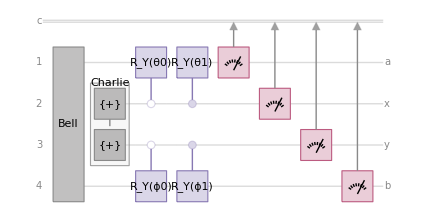

```mathematica
qc[θ0_,θ1_,ϕ0_,ϕ1_]:=QuantumCircuitOperator[{bell->{1,4},QuantumCircuitOperator[{"+"->{2,3}},"Charlie"],{"C0","RY"[θ0]->1,{2}},{"C","RY"[θ1]->1,{2}},{"C0","RY"[ϕ0]->4,{3}},{"C","RY"[ϕ1]->4,{3}},{1},{2},{3},{4}}];
qc[θ0,θ1,ϕ0,ϕ1]["Diagram","WireLabels"->{1->{1,Placed["a",Right]},2->{2,Placed["x",Right]},3->{3,Placed["y",Right]},4->{4,Placed["b",Right]}}]
```

Find the measurement probabilities of the above circuit.

```mathematica
FullSimplify[#,Assumptions->{{θ0,θ1,ϕ0,ϕ1}∈Reals}]&/@qc[θ0,θ1,ϕ0,ϕ1][]["Probabilities"]
```

<|0000→1/16 (1+Cos[θ0-ϕ0]),0001→1/8 Sin[(θ0-ϕ0)/2]^2,0010→1/16 (1+Cos[θ0-ϕ1]),0011→1/8 Sin[(θ0-ϕ1)/2]^2,0100→1/16 (1+Cos[θ1-ϕ0]),0101→1/8 Sin[(θ1-ϕ0)/2]^2,0110→1/16 (1+Cos[θ1-ϕ1]),0111→1/8 Sin[(θ1-ϕ1)/2]^2,1000→1/8 Sin[(θ0-ϕ0)/2]^2,1001→1/16 (1+Cos[θ0-ϕ0]),1010→1/8 Sin[(θ0-ϕ1)/2]^2,1011→1/16 (1+Cos[θ0-ϕ1]),1100→1/8 Sin[(θ1-ϕ0)/2]^2,1101→1/16 (1+Cos[θ1-ϕ0]),1110→1/8 Sin[(θ1-ϕ1)/2]^2,1111→1/16 (1+Cos[θ1-ϕ1])|>

Given all measurement results, check which ones are winning cases.

```mathematica
(BitXor[#1,#4]==BitAnd[#2,#3])&@@@Tuples[{0,1},4]
```

{True,False,True,False,True,False,False,True,False,True,False,True,False,True,True,False}

Pick only winning cases.

```mathematica
winningCases=Pick[Values[FullSimplify[#,Assumptions->{{θ0,θ1,ϕ0,ϕ1}∈Reals}]&/@qc[θ0,θ1,ϕ0,ϕ1][]["Probabilities"]],(BitXor[#1,#4]==BitAnd[#2,#3])&@@@Tuples[{0,1},4]]
```

{1/16 (1+Cos[θ0-ϕ0]),1/16 (1+Cos[θ0-ϕ1]),1/16 (1+Cos[θ1-ϕ0]),1/8 Sin[(θ1-ϕ1)/2]^2,1/16 (1+Cos[θ0-ϕ0]),1/16 (1+Cos[θ0-ϕ1]),1/16 (1+Cos[θ1-ϕ0]),1/8 Sin[(θ1-ϕ1)/2]^2}

Find the probability of winning.

```mathematica
proWinning=Total[winningCases]//FullSimplify
```

1/8 (4+Cos[θ0-ϕ0]+Cos[θ1-ϕ0]+Cos[θ0-ϕ1]-Cos[θ1-ϕ1])

Find the optimum rotation angle to win the game.

```mathematica
max=NMaximize[{proWinning,0\[VectorLessEqual]{θ0,θ1,ϕ0,ϕ1}\[VectorLessEqual]π},{θ0,θ1,ϕ0,ϕ1}]
```

{0.853553,{θ0→1.21042,θ1→2.78122,ϕ0→1.99582,ϕ1→0.425022}}

As one can see, with this quantum strategy, one can go beyond classical one.

## Another strategy (not useful)

We have the equation for winning probabilities. We would try random angles for R_Y gates of quantum circuit in this section. This section is useful in sense that even these angles must be optimized to see quantum advantage.

Create a function which incorporates different angles in the quantum circuit after the bell circuit. We have used additional R_y gates for this purpose.

```mathematica
quantumcirc[θ_,ϕ_]:=QuantumCircuitOperator[{"Bell",QuantumOperator[{"RY",θ},{1}],QuantumOperator[{"RY",ϕ},{2}],{1},{2}}]
```

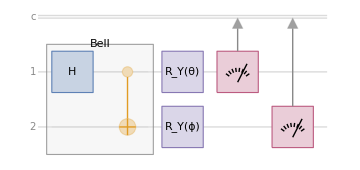

```mathematica
quantumcirc[θ,ϕ]["Diagram"]
```

Assuming the range of both angles to be from 0 to 2π, find the probabilities associated with different combination of quantum bits.

```mathematica
$Assumptions={0<=thetaA<=2π,0<=thetaB\[VectorLessEqual]2π};
prob=KeyMap[#["Name"]&][FullSimplify/@quantumcirc[thetaA,thetaB][]["Probabilities"]]
```

<|{0,0}→1/4 (1+Cos[thetaA-thetaB]),{0,1}→1/4 (1-Cos[thetaA-thetaB]),{1,0}→1/4 (1-Cos[thetaA-thetaB]),{1,1}→1/4 (1+Cos[thetaA-thetaB])|>

Define it as probability distribution.

```mathematica
𝒟=ProbabilityDistribution[Which@@Sequence@@@Append[KeyValueMap[{{a,b}==#1,#2}&][prob],{True,0}],{a,0,∞,1},{b,0,∞,1}];
```

Check that the results are only 0 and 1

```mathematica
PDF[𝒟,{-1,2}]
```

0

Check 𝒟 reproduces probabilities(trivial, as expected) show above.

```mathematica
AssociationMap[PDF[𝒟,#]&,Tuples[{0,1},2]]==prob
```

True

Find the winning probabilities.

```mathematica
win=Simplify@Expectation[Boole[BitXor[a,b]==BitAnd[x,y]],{{x,y}\[Distributed]DiscreteUniformDistribution[{{0,1},{0,1}}],{a,b}\[Distributed]𝒟}]
```

1/4 (2+Cos[thetaA-thetaB])

Find the maxima and angles associated in terms of π.

```mathematica
NMaximize[{win,0\[VectorLessEqual]{thetaA,thetaB}\[VectorLessEqual]π},{thetaA,thetaB}];
%/. Rule[a_,b_]:>Rule[a,Rationalize[b/Pi,.01]]
```

{0.75,{thetaA→7/10,thetaB→7/10}}

This is definitely equal to optimal classical strategy, therefore we need to change our strategy of choosing random angle for the optimal quantum strategy.

## Initialization cells

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

## References

https://www.scottaaronson.com/qclec/14.pdf

https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.49.91

https://en.wikipedia.org/wiki/Tsirelson%27s_bound

## CITE THIS NOTEBOOK

CHSH Game: illustrating the peculiar advantages of quantum strategies over classical ones
by Shivam Sawarn
Wolfram Community, STAFF PICKS, October 16, 2023
https://community.wolfram.com/groups/-/m/t/3036763